```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/412nm.dat"]
```

{{1.50189,-0.0930477},{1.45414,-0.0814487},{1.33983,-0.042417},{1.30748,-0.0303974},{1.27821,-0.0159566},{1.24682,-0.05261},{1.22351,-0.147155},{1.20659,-0.226938},{1.18213,-0.353281},{1.16419,-0.483032},{1.15263,-0.554238},{1.13304,-0.634067},{1.09662,-0.0372866},{1.09807,-0.093992},{1.10207,-0.0932343},{1.10747,-0.0856995},{1.11401,-0.0878481},{1.12685,-0.0585405},{1.13867,-0.0439937},{1.15401,-0.039937},{1.16573,-0.0667169},{1.20258,-0.0664176},{1.26466,-0.0800394},{1.30748,-0.0852638},{1.33983,-0.122914},{1.37936,-0.143593}}

-0.54671+0.326992 x

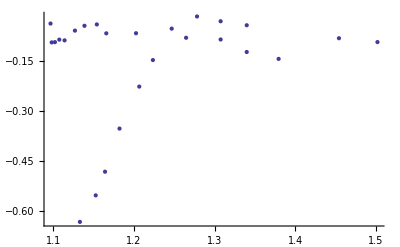

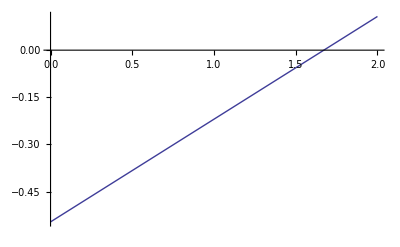

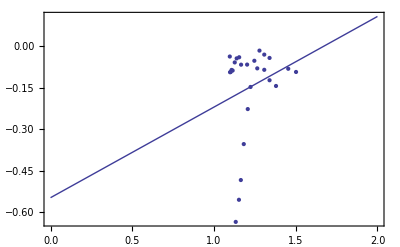

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```